```mathematica
Subscript[ϕ, n_][x_] = 1/π^(1/4)/Sqrt[2^n*Factorial[n]] * HermiteH[n,x]*E^(-x^2/2);
b[t_]=Sqrt[1+t^2];
τ[t_]=ArcTan[t];
Subscript[Φ, n_][x_,t_]=b[t]^(-1/2)Subscript[ϕ, n][x/b[t]]*E^(I*(x^2*b'[t]/(2*b[t])-(n+1/2)τ[t]));
t ≥0;
Subscript[ψ, F][x_,y_,t_] = 1/Sqrt[2] * (Subscript[Φ, 0][x,t]Subscript[Φ, 1][y,t] - Subscript[Φ, 0][y,t]Subscript[Φ, 1][x,t] );
Subscript[ψ, B][x_,y_,t_]=Sign[y-x]Subscript[ψ, F][x,y,t];
Subscript[ρ, F][x_,y_]=Integrate[Subscript[ψ, F][x,Subscript[x, 2],0]*Subscript[ψ, F][y,Subscript[x, 2],0],{Subscript[x, 2],-Infinity,Infinity}];
Subscript[n, F][p_] = 2/(2*π)*Integrate[E^(-I*p*(y-x))*Subscript[ρ, F][x,y],{x,-∞, ∞},{y,-∞, ∞}];
ρ[x_,y_]=Subscript[ρ, F][x,y]-2*Sign[y-x]Integrate[Subscript[ψ, F][x,Subscript[x, 2],0]*Subscript[ψ, F][y,Subscript[x, 2],0],{Subscript[x, 2],x,y}];
Subscript[ρ, B][x_,y_,t_]=1/b[t]*ρ[x/b[t],y/b[t]]*E^(-I*(b'[t](x^2-y^2))/(2*b[t]));
Subscript[n, B][p_,t_] := 2/(2π)*NIntegrate[E^(I*p*(x-y))Subscript[ρ, B][x,y,t],{x,-∞, ∞},{y,-∞, ∞},Method->{"LocalAdaptive", Method->"CartesianRule"}, AccuracyGoal->5,PrecisionGoal->5];
```

```mathematica
Pdomain=Union[Range[0,2,1/4],Range[2,4,1/2]];
Tdomain = {0,0.25,.5,0.75,1,1.5,2,2.5,3,3.5,4,5,6,7,8,9,10,12};
(* Set interopolation functions for various points in time *)
Subscript[dataSet, m_]:=Re[Subscript[n, B][Pdomain,Tdomain[[m]] ]];
Do[Subscript[dataSet, i]=Subscript[dataSet, i],{i,1,Length[Tdomain]}]
```

```mathematica
Do[Print[Subscript[dataSet, i]],{i,1,Length[Tdomain]}]
```

{1.13796,1.04414,0.80953,0.539255,0.324503,0.196915,0.136335,0.107018,0.0850291,0.0432128,0.0170794,0.00674174,0.0031523}

{1.11109,1.02159,0.797934,0.540387,0.335247,0.211612,0.149753,0.116234,0.0896289,0.0424595,0.0157199,0.00599175,0.00280476}

{1.04385,0.965458,0.769846,0.544704,0.363625,0.249192,0.183037,0.138033,0.0994482,0.0396049,0.0123286,0.00434361,0.00207094}

{0.962183,0.897924,0.737867,0.553274,0.401229,0.296176,0.222239,0.161284,0.107591,0.0345689,0.00855635,0.00281813,0.00140095}

{0.884879,0.834869,0.710381,0.565504,0.440297,0.341439,0.256861,0.178793,0.110893,0.028883,0.00570668,0.00181695,0.000932774}

{0.767333,0.741393,0.675968,0.594077,0.50634,0.408843,0.300513,0.194004,0.107553,0.0207907,0.00303485,0.000858345,0.000431482}

{0.694599,0.68584,0.661276,0.619504,0.550324,0.446207,0.318564,0.195433,0.101855,0.0173928,0.00215942,0.000471364,0.000222486}

{0.650552,0.653575,0.656033,0.638389,0.57706,0.465198,0.324943,0.193675,0.098143,0.016081,0.00179287,0.000295895,0.000125626}

{0.62335,0.634402,0.654655,0.651466,0.593014,0.474838,0.327008,0.191941,0.0960946,0.0155053,0.00161088,0.000208169,0.0000797353}

{0.606021,0.622601,0.654711,0.660346,0.602674,0.47992,0.327596,0.190716,0.094967,0.0152061,0.00151408,0.000160106,0.0000610433}

{0.594612,0.615064,0.655222,0.666394,0.6087,0.482742,0.3277,0.189914,0.0943179,0.0150471,0.00145154,0.000128666,0.0000265471}

{0.581517,0.606679,0.656363,0.673519,0.615207,0.485408,0.327565,0.189044,0.0936695,0.0148899,0.00137892,0.000110952,0.0000195887}

{0.574867,0.60256,0.657248,0.677208,0.618289,0.486516,0.327416,0.188577,0.0933185,0.0148067,0.00136839,0.0000386111,-0.0000959582}

{0.571178,0.60034,0.657746,0.679249,0.619863,0.487028,0.327309,0.188389,0.0932605,0.0145789,0.00134376,0.0000324082,-0.0000940196}

{0.569002,0.599077,0.658177,0.680441,0.62074,0.48733,0.327241,0.188291,0.0931932,0.0147488,0.00133138,3.49333×10^-7,-0.000129723}

{0.567357,0.598196,0.658259,0.681255,0.621364,0.487513,0.327146,0.188172,0.0929605,0.0146827,0.00136776,0.000112418,0.000451532}

{0.566657,0.597628,0.65864,0.681883,0.621692,0.487999,0.327092,0.188062,0.0932055,0.0146378,0.00134915,-0.000107665,-0.000755554}

{0.565602,0.597107,0.658737,0.682287,0.621959,0.487756,0.326975,0.18809,0.0929126,0.0140748,0.00137851,0.000205564,-0.0000997856}

```mathematica
Subscript[dataSet, 1]={1.1379588318766027,1.0441397640173031,0.8095299907043565,0.5392545812626595,0.32450252366745536,0.19691493862478998,0.1363345503520609,0.10701776554323943,0.08502907386766,0.0432128435498675,0.01707943252224098,0.006741735325094581,0.0031523033820538794};
Subscript[dataSet, 2]={1.1110886876330863,1.0215942329367909,0.7979342823102873,0.5403870138061999,0.3352473255206777,0.21161211919706932,0.14975272161523423,0.11623389734925557,0.08962890690734887,0.04245950917838006,0.015719890485684913,0.005991750279227949,0.002804756140916823};
Subscript[dataSet, 3]={1.0438526706044056,0.9654582247272511,0.7698457188100407,0.5447044586698063,0.363625124575934,0.24919238450304876,0.18303727200825362,0.13803288293881374,0.09944818896738095,0.03960489183505136,0.01232857292752953,0.004343614081098863,0.002070944445036076};
Subscript[dataSet, 4]={0.9621826459986196,0.8979238745218086,0.7378668993337009,0.5532735929063574,0.40122943433321184,0.2961764969756655,0.22223896459521636,0.161283951091721,0.10759094834001451,0.034568887533099245,0.008556346889278208,0.0028181331557041427,0.0014009483731097538};
Subscript[dataSet, 5]={0.8848789102222434,0.8348688891921924,0.7103810958667275,0.5655040780515793,0.4402966453503231,0.3414391144015064,0.2568608054448787,0.1787932342737168,0.11089332640876783,0.02888300131875195,0.005706677752523128,0.0018169526245021513,0.0009327740319620668};
Subscript[dataSet, 6]={0.7673327683576631,0.7413929406735889,0.6759676613404968,0.5940766050234464,0.5063395868476968,0.40884333218201396,0.3005133494017972,0.1940035218762424,0.10755307565805797,0.02079066334737399,0.003034849459615799,0.0008583448225448991,0.00043148221792101447};
Subscript[dataSet, 7]={0.6945986343612388,0.6858404122198555,0.6612761400838048,0.6195040783518152,0.550323603264442,0.4462072586473096,0.3185635383131019,0.19543323950391517,0.10185457107669638,0.017392775960006962,0.0021594224089967013,0.0004713637860050032,0.0002224857409678804};
Subscript[dataSet, 8]={0.6505521739729583,0.6535750897827107,0.6560326329134171,0.6383894449265362,0.5770602804658989,0.4651982646309006,0.32494253384761673,0.19367486453893734,0.0981429825946128,0.016081026090161002,0.0017928715191675275,0.0002958949713898308,0.00012562641101777165};
Subscript[dataSet, 9]={0.6233496476644133,0.6344019414936374,0.654655488286419,0.6514660853162555,0.5930136661901273,0.4748384393730299,0.3270081301534015,0.19194126635509637,0.09609457835593424,0.015505269215310834,0.0016108810629226304,0.00020816855379144586,0.00007973527293371036};
Subscript[dataSet, 10]={0.6060210883586838,0.6226006203011243,0.6547110092674896,0.6603464388411968,0.60267361578455,0.47992032021215897,0.3275959588648342,0.19071574297738775,0.09496701259833162,0.015206086012140217,0.001514080090140727,0.00016010582023139372,0.0000610432810734303};
Subscript[dataSet, 11]={0.5946123537261836,0.6150643979367901,0.6552221255206788,0.6663935442368689,0.6087004981845491,0.4827416499385969,0.32770010780156705,0.1899140637623699,0.0943179194887916,0.015047082872451384,0.001451543208095667,0.00012866556504180515,0.000026547051251666673};
Subscript[dataSet, 12]={0.581517496903436,0.6066791772311282,0.6563628789695631,0.6735187129288857,0.6152065222396395,0.48540849580444,0.3275652137679446,0.18904439442971666,0.09366948285498863,0.014889946312993861,0.0013789247825858131,0.00011095198653096013,0.000019588745537299088};
Subscript[dataSet, 13]={0.574867308574481,0.6025596739967781,0.6572481235689512,0.6772079743665025,0.6182888216222535,0.4865156899221342,0.32741649314620885,0.18857739525781936,0.09331845199028115,0.014806687624681136,0.00136839146324681,0.000038611072216150886,-0.00009595824874487513};
Subscript[dataSet, 14]={0.5711775049114358,0.6003403151912421,0.6577464901339536,0.6792486298954008,0.6198633762978748,0.48702822902119886,0.3273091372320608,0.18838879866504044,0.09326047768323285,0.014578893304061744,0.0013437646299347163,0.0000324081851977304,-0.00009401964376889709};
Subscript[dataSet, 15]={0.5690017429452354,0.5990769010431481,0.6581773638831588,0.6804408254776313,0.6207400823760135,0.48733006409625224,0.3272410014321825,0.188290882801423,0.09319321734902264,0.014748835118679363,0.0013313822033287897,3.493326522051784*^-7,-0.00012972272257372967};
Subscript[dataSet, 16]={0.5673569763236354,0.5981961042501563,0.6582594273574671,0.6812549065021685,0.6213640707719953,0.48751321810335324,0.32714609894642716,0.1881717541663747,0.09296050501983319,0.014682681108357624,0.0013677606420342272,0.00011241778502424256,0.0004515315324206942};
Subscript[dataSet, 17]={0.5666569356520894,0.5976279396404304,0.6586399513603383,0.6818832231904036,0.6216924680138382,0.4879991435375497,0.3270915147058346,0.18806181040828582,0.09320554615447663,0.01463780911928932,0.001349151358000914,-0.00010766517185865455,-0.0007555541825406411};
Subscript[dataSet, 18]={0.5656019855362622,0.5971071365080196,0.65873732080903,0.6822869722393502,0.6219592574000945,0.48775553042052006,0.32697456594045765,0.18809049160373395,0.09291263136882692,0.014074819880363281,0.0013785070776517814,0.00020556369671651556,-0.00009978557315142571};
```

```mathematica
(* Prepare domains and ranges for plotting*)
FullD=Flatten[Prepend[Take[Pdomain,-Length[Pdomain]+1],Reverse[-1*Pdomain]]];
Do[Subscript[FullR, i]=Flatten[Prepend[Take[Subscript[dataSet, i],-Length[Subscript[dataSet, i]]+1],Reverse[Subscript[dataSet, i]]]],{i,1,Length[Tdomain]}];
(* create list of interpolated functions for plotting purposes *)
Do[Subscript[f, i]=Interpolation[Thread[{FullD,Subscript[FullR, i]}] ],{i,1,Length[Tdomain]}]
```

```mathematica
frame[i_]:=Show[Plot[{Subscript[f, i][x],Subscript[n, F][x]},{x,-4,4},PlotRange->{0,1.2},PlotStyle -> {Default,Dashed},PlotLabel->"Momentum Distribution: Expanding Gas of HCB",AxesLabel->{"p","n(p,t)"},ImageSize->Scaled[1]],Graphics[Text[StringForm["t = ``",Tdomain[[i]]],{2,1},{0,0}]]];
frames=Table[frame[i],{i,1,Length[Tdomain]}];
```

```mathematica
Export["C:/Users/Tim/Documents/PhysicsResearch/UltraColdAtoms/ExpandingGas.gif",frames,AnimationRepetitions->Infinity,"DisplayDurations"-> .25];
```

Export::nodir: Directory C:\Users\Tim\Documents\PhysicsResearch\UltraColdAtoms\ does not exist.

Export::noopen: Cannot open C:/Users/Tim/Documents/PhysicsResearch/UltraColdAtoms/ExpandingGas.gif.

```mathematica
Tdomain = {0,0.25,.5,1,2,3,4,8,12};
Subscript[dataSet, 1]={1.1379588318766027,1.0441397640173031,0.8095299907043565,0.5392545812626595,0.32450252366745536,0.19691493862478998,0.1363345503520609,0.10701776554323943,0.08502907386766,0.0432128435498675,0.01707943252224098,0.006741735325094581,0.0031523033820538794};
Subscript[dataSet, 2]={1.1110886876330863,1.0215942329367909,0.7979342823102873,0.5403870138061999,0.3352473255206777,0.21161211919706932,0.14975272161523423,0.11623389734925557,0.08962890690734887,0.04245950917838006,0.015719890485684913,0.005991750279227949,0.002804756140916823};
Subscript[dataSet, 3]={1.0438526706044056,0.9654582247272511,0.7698457188100407,0.5447044586698063,0.363625124575934,0.24919238450304876,0.18303727200825362,0.13803288293881374,0.09944818896738095,0.03960489183505136,0.01232857292752953,0.004343614081098863,0.002070944445036076};
Subscript[dataSet, 4]={0.8848789102222434,0.8348688891921924,0.7103810958667275,0.5655040780515793,0.4402966453503231,0.3414391144015064,0.2568608054448787,0.1787932342737168,0.11089332640876783,0.02888300131875195,0.005706677752523128,0.0018169526245021513,0.0009327740319620668};
Subscript[dataSet, 5]={0.6945986343612388,0.6858404122198555,0.6612761400838048,0.6195040783518152,0.550323603264442,0.4462072586473096,0.3185635383131019,0.19543323950391517,0.10185457107669638,0.017392775960006962,0.0021594224089967013,0.0004713637860050032,0.0002224857409678804};
Subscript[dataSet, 6]={0.6233496476644133,0.6344019414936374,0.654655488286419,0.6514660853162555,0.5930136661901273,0.4748384393730299,0.3270081301534015,0.19194126635509637,0.09609457835593424,0.015505269215310834,0.0016108810629226304,0.00020816855379144586,0.00007973527293371036};
Subscript[dataSet, 7]={0.5946123537261836,0.6150643979367901,0.6552221255206788,0.6663935442368689,0.6087004981845491,0.4827416499385969,0.32770010780156705,0.1899140637623699,0.0943179194887916,0.015047082872451384,0.001451543208095667,0.00012866556504180515,0.000026547051251666673};
Subscript[dataSet, 8]={0.5690017429452354,0.5990769010431481,0.6581773638831588,0.6804408254776313,0.6207400823760135,0.48733006409625224,0.3272410014321825,0.188290882801423,0.09319321734902264,0.014748835118679363,0.0013313822033287897,3.493326522051784*^-7,-0.00012972272257372967};
Subscript[dataSet, 9]={0.5656019855362622,0.5971071365080196,0.65873732080903,0.6822869722393502,0.6219592574000945,0.48775553042052006,0.32697456594045765,0.18809049160373395,0.09291263136882692,0.014074819880363281,0.0013785070776517814,0.00020556369671651556,-0.00009978557315142571};
```

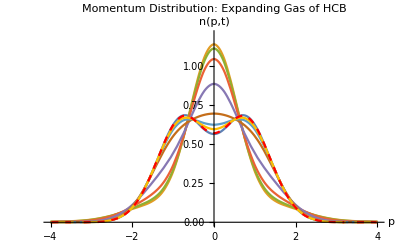

C:/Users/Tim/Documents/PhysicsResearch/UltraColdAtoms/Plots/MomDistExpandingTG.png

```mathematica
FuncList=Join[{Subscript[n, F][x]},Array[Subscript[f, #][x]&,Length[Tdomain]-1,1]];
p2=Plot[FuncList,{x,-4,4},PlotRange->{0,1.2},PlotLabel->"Momentum Distribution: Expanding Gas of HCB",AxesLabel->{"p","n(p,t)"},ImageSize->Scaled[1.8],
PlotStyle->{Default,Default,Default,Default,Default,Default,Default,Default,{Dashed,Red}}]
Export["C:/Users/Tim/Documents/PhysicsResearch/UltraColdAtoms/Plots/MomDistExpandingTG.png",p2]
```